# Project - Sampling Methods

SCIMATH202 - Theory of Statistics and Data Analysis
Joanikij Chulev
24.04.2023

## Uniform distribution

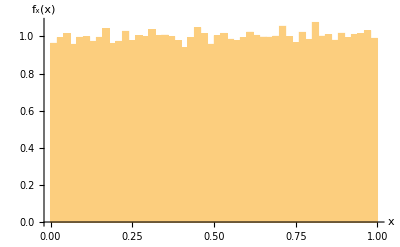

```mathematica
(*This code is to show how to generate and demonstrate the uniform distribution*)
uniform=RandomReal[{0,1},{10^5}];(*Generate a sample from the uniform distribution*)

(*Create a histogram of the sample*)
Histogram[uniform,{0,1,1/50},"PDF",AxesLabel->{"x","f_x(x)"}]
```

## Geometric distribution-transforming the uniform sample to geometric

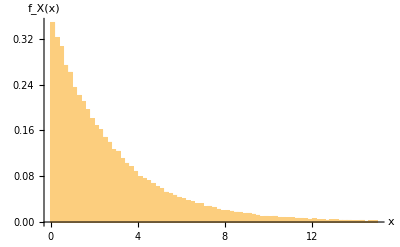

```mathematica
p=0.3;  (*Probability of success for the geometric distribution*)
uniform=RandomReal[{0,1},{10^5}]; (*Generate a sample from the uniform distribution*)

(*Convert the sample to a sample of the geometric distribution*)
geometric=Log[1-uniform]/Log[1-p]; 
(*Create a histogram of the sample*)
Histogram[geometric,{0,15,1/5},"PDF",AxesLabel->{"x","f_X(x)"}]
```

## Bernoulli distribution-transforming the uniform sample to Bernoulli

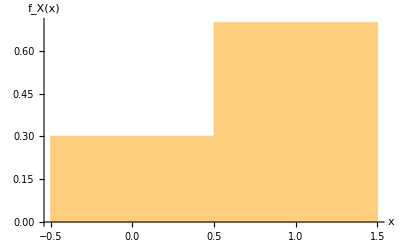

```mathematica
p=0.7; (*Probability of success for the Bernoulli distribution*)
uniform=RandomReal[{0,1},{10^5}]; (*Generate a sample from the uniform distribution*)

(*Convert the sample to a sample of the Bernoulli distribution*)
Bernoulli=Boole[#<=p]&/@uniform;
(*Create a histogram of the sample*)
Histogram[Bernoulli,{-0.5,1.5,1},"PDF",AxesLabel->{"x","f_X(x)"}]
```

## Binomial distribution-transforming the Bernoulli sample to binomial

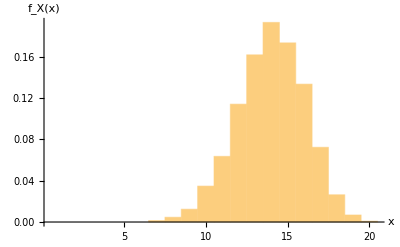

```mathematica
n = 20; (* Number of trials *)
p = 0.7; (* Probability of success for the Bernoulli distribution *)

(* Convert the sample to a sample of the binomial distribution *)
x = Bernoulli; (* Use the previously generated Bernoulli sample *)
binomial = Table[Total[Take[x, {n*(i-1)+1, n*i}]], {i, 1, Length[x]/n}];

(* Create a histogram of the sample *)
Histogram[binomial, {0.5, n+0.5, 1}, "PDF",AxesLabel->{"x","f_X(x)"}]
```

## Exponential distribution-transforming the uniform sample to exponential

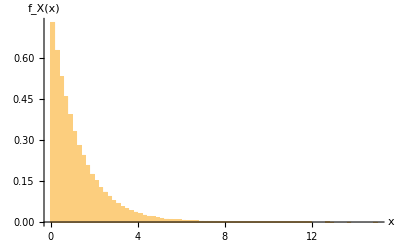

```mathematica
λ=0.8;(* Set lambda *)
uniform=RandomReal[{0,1},{10^5}];(*Generate a sample from the uniform distribution*)

(* Convert the sample to a sample of the exponential distribution *)
exponential=-Log[1-uniform]/λ;

(* Create a histogram of the sample *)
Histogram[exponential,{0,15,1/5},"PDF",AxesLabel->{"x","f_X(x)"}]
```

## Uniform distribution-transforming the exponential sample to uniform

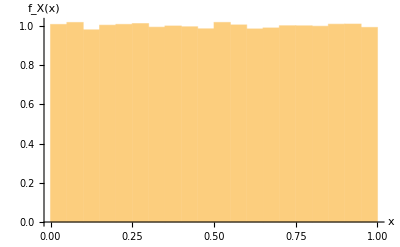

```mathematica
λ=2.5; (* Set lambda *)
exponentialsample=RandomReal[ExponentialDistribution[λ],{10^5}];(*Generate a sample from the exponential distribution*)

(* Convert the sample to a sample of the uniform distribution *)
getuniform=1-Exp[-λ exponentialsample];

(* Create a histogram of the sample *)
Histogram[getuniform,{0,1,1/20},"PDF",AxesLabel->{"x","f_X(x)"}]
```

## Normal distribution-transforming the uniform sample to normal using BOX-MULLER TRANSFORM

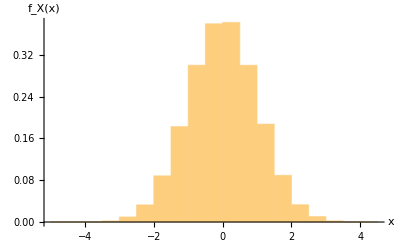

```mathematica
(* This converts the sample of the uniform distribution to a sample of the normal distribution: *)
μ=0; (*Mean of the normal distribution*)
σ=1; (*Standard deviation of the normal distribution*)
sample={}; (*Initialize empty list for the sample*)
While[Length[sample]<10^5,(*Draw 100000 samples*)u1=RandomReal[];(*Generate first random value from the uniform distribution*)u2=RandomReal[];(*Generate second random value from the uniform distribution*)x=Sqrt[-2 Log[u1]] Cos[2 Pi u2];(*Compute the Box-Muller transform*)z=μ+σ x;(*Transform to a sample from the normal distribution*)AppendTo[sample,z] (*Add the sample to the list*)]
normaldist=sample;
Histogram[normaldist,Automatic,"PDF",AxesLabel->{"x","f_X(x)"}](*Create histogram of sample from the normal distribution*)
```

## Beta distribution-transforming the uniform samples to beta

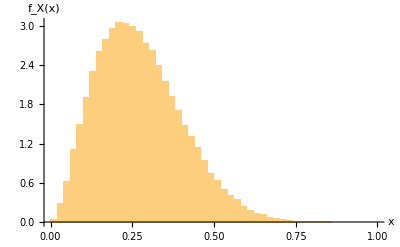

```mathematica
a=2; (*Shape parameter alpha*)
b=8; (*Shape parameter beta*)

sample={}; (*Initialize empty list for the sample*)

While[Length[sample]<10^5,u1=RandomReal[];(*Generate first random value from the uniform distribution*)u2=RandomReal[];(*Generate second random value from the uniform distribution*)x=u1^(1/a);(*Transform u1 to a sample from the candidate distribution*)y=u2 x^(a-1) (1-x)^(b-1);(*Compute the acceptance probability*)If[RandomReal[]<y,AppendTo[sample,x]] (*Accept the sample with probability y*)]
beta=sample;
Histogram[beta,{0,1,1/50},"PDF",AxesLabel->{"x","f_X(x)"}] (*Create histogram of sample from the beta distribution*)
```

## Gamma distribution-transforming the beta sample to gamma

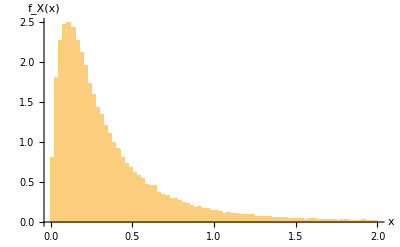

```mathematica
a=2; (*Shape parameter alpha*)
b=3; (*Shape parameter beta*)
(*Generate a list of 100,000 random numbers from a beta distribution with parameters alpha and beta*)
betaDist=RandomVariate[BetaDistribution[a,b],10^5];
(*Transform the random numbers a to get the y-values for beta prime*)
y=betaDist/(1-betaDist);
(*Set alphaNew to alpha*)
alphaNew=a;
(*Set betaNew to beta+alpha*)
betaNew=b+a;
(*Set the value of k to alphaNew*)
k=alphaNew;
(*Calculate the value of theta using the formula 1/betaNew*)
theta=1/betaNew;
(*Create a list of gamma values using the mathematical formula theta*y*k*)
gammaDist=Table[theta*y[[i]]*k,{i,Length[betaDist]}];
(*Create a histogram of the gamma values *)
Histogram[gammaDist,{0,2,1/40},"PDF",AxesLabel->{"x","f_X(x)"}]
```

## Normal distribution-transforming the uniform sample to normal using Monte Carlo Accept–Reject Method

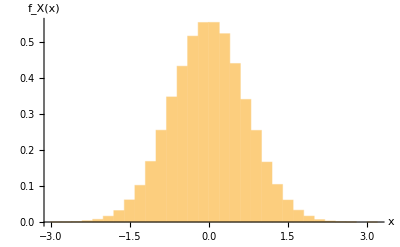

```mathematica
(*accept-reject sampling method- MONTE CARLO METHOD *)
μ=0; (*Mean of the normal distribution*)
σ=1; (*Standard deviation of the normal distribution*)
sample={}; (*Initialize empty list for the sample*)
While[Length[sample]<10^5,(*Draw 100000 samples*)x=μ+σ RandomReal[NormalDistribution[]];(*Generate a sample from the normal distribution*)u=RandomReal[];(*Generate a sample from the uniform distribution*)If[u<=PDF[NormalDistribution[],x]/PDF[UniformDistribution[{0,1}],u*σ+μ],AppendTo[sample,x]]; (*Accept or reject the sample based on the ratio of the normal PDF to the uniform PDF*)]
Histogram[sample,Automatic,"PDF",AxesLabel->{"x","f_X(x)"}] (*Plot the histogram of the resulting sample*)
```

## Normal distribution-transforming the uniform sample to normal using Central Limit Theorem

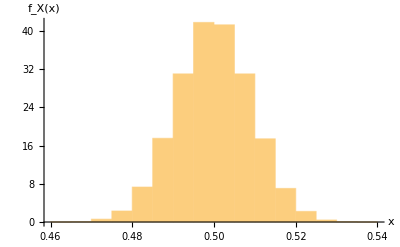

```mathematica
n=1000;(*Set the number of distributions to average*)
numDists=10^5;(*Set the number of distributions to average*)
(*Generate numDists samples of n random numbers from a uniform distribution between 0 and 1*)
samples=RandomReal[1,{numDists,n}];
(*Calculate the mean of each sample*)
means=Mean/@samples;
(*Calculate the standard deviation of the sample means*)
sd=StandardDeviation[means];
(*Calculate the standard error of the sample means*)
se=sd/Sqrt[n];
(*Create a normal distribution with mean equal to the average of the sample means and standard deviation equal to the standard error*)
dist=NormalDistribution[Mean[means],se];
(*Plot a histogram of the sample means and the normal distribution*)
Histogram[means,Automatic,"PDF",AxesLabel->{"x","f_X(x)"}]
```

## Negative binomial distribution-transforming the Bernoulli sample to negative binomial

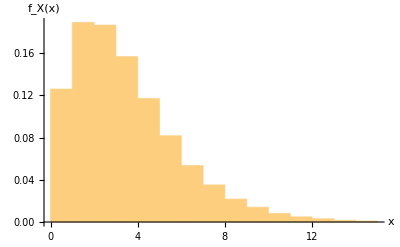

```mathematica
p=0.5; (*probability of success*)
r=3;   (*The negative binomial distribution has an r of 3*)
Negbinomial={};
nsamples=10^5; (*number of samples to generate*)
(*Generate Bernoulli trials and count the number of failures until r successes are reached*)
For[ii=1,ii<=nsamples,ii++,failures=0;
successes=0;
While[successes<r,trial=RandomReal[];
If[trial<=p,successes++,failures++];];
AppendTo[Negbinomial,failures];]

(*Plot the histogram*)
Histogram[Negbinomial,{0,15,1},"PDF",AxesLabel->{"x","f_X(x)"}]
```

## Poisson distribution-transforming the exponential sample to Poisson

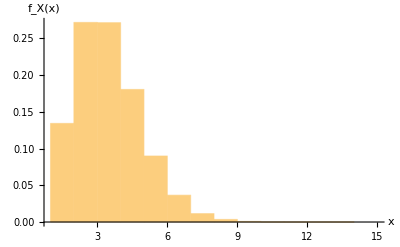

```mathematica
λ=2; (*Set the rate parameter for the exponential distribution*)
sax={}; (*Initialize empty list for the Poisson sample*)
sum=0; (*Initialize the sum to 0*)
count=0; (*Initialize the count to 0*)
While[Length[sax]<10^5,(*Draw 100000 samples*)x=RandomVariate[ExponentialDistribution[λ]];(*Generate a sample from the exponential distribution*)sum+=x;(*Add the sample to the sum*)count++;(*Increment the count*)If[sum>=1,(*If the sum is greater than or equal to 1*)AppendTo[sax,count];(*Append the count to the list of samples*)sum=0;(*Reset the sum to 0*)count=0; (*Reset the count to 0*)]]

(*Plot a histogram of the Poisson sample*)
Histogram[sax,{1,15,1},"PDF",AxesLabel->{"x","f_X(x)"}]
```